### Init

```mathematica
n=4;
g=GridGraph[{n,n}];
```

```mathematica
temperatureTable=Table[RandomReal[],n^2];

initialCircleCondition={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

hg={{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,27},{28,29},{28,36},{29,21},{29,28},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,25},{33,34},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,43},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}};
```

```mathematica
k=0.1;δt=0.5;
```

```mathematica
ruleSet=ResourceFunction["EnumerateWolframModelRules"][{{2,2}}->{{2,2}}];
```

ResourceObject::updav: There is an update available for resource "ParallelMapMonitored". Use ResourceUpdate[ParallelMapMonitored] to get the update.

```mathematica
graphToHypergraphNew[g_]:=Flatten[DeleteCases[Table[If[(Normal@AdjacencyMatrix@g)[[#]][[i]]*i==0,0,{#,i}],{i,VertexList@g}],0]&/@(VertexList@g),1]

rwLaplacian[g_]:=IdentityMatrix[Length@VertexList@g]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@g],Normal@AdjacencyMatrix[g]]

dynamicDiscreteLaplacian[G_,ϕ_]:=Dot[IdentityMatrix[Length@VertexList@G]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@G],Normal@AdjacencyMatrix[G]],ϕ]

EulerMethod489[{HG_,t_,ϕ_}]:={ResourceFunction["WolframModel"][#,HG,1,"FinalState"]&[ruleSet[[489]]],t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 


listEvolution[r_,InitialCondition_]:=NestWhileList[
ResourceFunction["WolframModel"][r,#1,1,"FinalState"]&,
InitialCondition,
(!IsomorphicGraphQ[SimpleGraph@Graph[UndirectedEdge@@@#1],SimpleGraph@Graph[UndirectedEdge@@@#2]]&&ResourceFunction["ConnectedHypergraphQ"][#1])& ,
2,100
]

EulerMethodStatic[{HG_,t_,ϕ_}]:={HG,t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]}
```

```mathematica
InitialConditionFullyConnected=Tuples[Range[n^2],2];
```

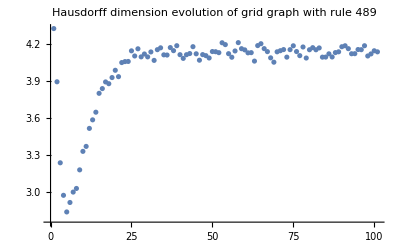

```mathematica
ListPlot[hausdorffDimension489,PlotRange->All,PlotLabel->"Hausdorff dimension evolution of grid graph with rule 489"]
```

```mathematica
hausdorffDimension489=Module[{rule=ruleSet[[489]]},ResourceFunction["WolframHausdorffDimension"][SimpleGraph[Graph[UndirectedEdge@@@#]],All,{1,1},"VertexMethod"->Mean]&/@listEvolution[rule,InitialConditionFullyConnected]]
```

{4.32193,3.89068,3.23416,2.97072,2.83592,2.91261,2.99696,3.02628,3.17686,3.32691,3.36709,3.51302,3.5822,3.64424,3.79718,3.83551,3.88951,3.87516,3.92493,3.98392,3.93224,4.04644,4.05436,4.05547,4.14147,4.09984,4.15799,4.0927,4.11596,4.09264,4.13264,4.0641,4.15092,4.16595,4.10899,4.10742,4.16791,4.14292,4.18311,4.11025,4.08037,4.11022,4.1195,4.17519,4.11754,4.06565,4.11095,4.10251,4.0836,4.13577,4.13434,4.12674,4.20703,4.19196,4.11853,4.08954,4.14051,4.2081,4.15894,4.14927,4.12529,4.12685,4.0583,4.18396,4.19921,4.15947,4.1351,4.08464,4.04948,4.13365,4.14265,4.15169,4.09044,4.15114,4.18244,4.13577,4.10251,4.17278,4.08323,4.15039,4.16724,4.15019,4.16512,4.0904,4.09099,4.1173,4.0918,4.12727,4.13362,4.17479,4.18264,4.15909,4.11791,4.11847,4.15207,4.15081,4.18291,4.09983,4.11664,4.14208,4.13327}

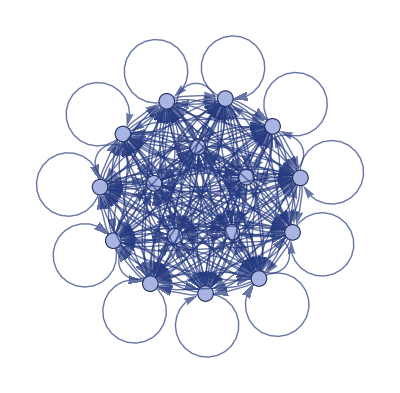

```mathematica
ResourceFunction["WolframModelPlot"][InitialConditionFullyConnected]
```

```mathematica
Graph[UndirectedEdge@@@InitialConditionFullyConnected, VertexStyle->Thread[Range[n^2]->ColorData["TemperatureMap"]/@temperatureTable],VertexSize->.5]
```

-Graphics-

```mathematica
hGSeries = NestList[EulerMethod489,{InitialConditionFullyConnected,0,temperatureTable},200]
```

{{1},{1},197,{{{7,6},{10,2},{6,8},{8,12},{12,15},{16,3},{13,11},{10,5},{10,4},{16,9},{9,7},{7,13},{10,3},{3,15},{15,4},{4,14},{1,14},{14,9},{13,9},{9,6},{6,11},{11,5},{10,5},{5,1},{14,5},{5,5},{14,5},{5,4},{5,8},{8,10},{8,4},{4,14},{3,5},190,{3,2},{8,2},{2,14},{10,3},{3,7},{6,7},{7,3},{8,3},{3,9},{9,14},{14,11},{4,7},{7,10},{6,8},{8,7},{6,15},{15,10},{11,10},{10,8},{2,8},{8,16},{6,2},{2,8},{15,6},{6,16},{11,3},{3,13},{9,11},{11,4},{4,7},{7,10},{4,1},{1,16}},99.5,{1}},1}
 |  |  |  |

```mathematica
complexEigenSeries = N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]];
```

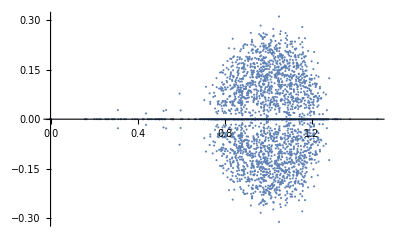

```mathematica
summaryEigenPlot = ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Flatten@complexEigenSeries]
```

```mathematica
laplacianSeries = rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]];
```

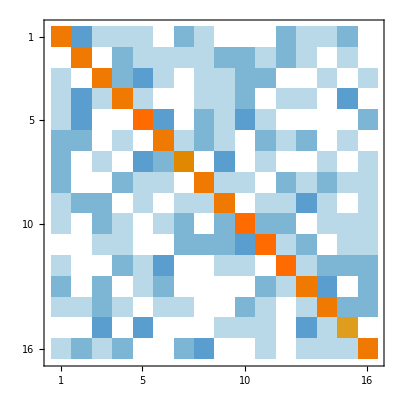

```mathematica
MatrixPlot@laplacianSeries[[92]]
```

```mathematica
lt = Dot[laplacianSeries[[2]],PseudoInverse[laplacianSeries[[1]]]]
```

{{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/16,15/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16},{0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0},{-1/16,-1/16,-1/16,15/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16},{0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0},{-1/16,-1/16,-1/16,-1/16,-1/16,15/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16},{0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0},{-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,15/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16},{0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0},{-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,15/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16},{0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0},{-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,15/16,-1/16,-1/16,-1/16,-1/16},{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0},{-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,15/16,-1/16,-1/16},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1},{-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,15/16}}

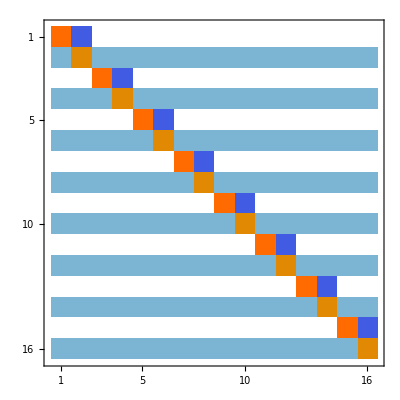

```mathematica
MatrixPlot[lt]
```

```mathematica
MatrixPlot@Dot[lt,laplacianSeries[[1]]];
MatrixPlot@laplacianSeries[[2]];
```

```mathematica
lt2 = Dot[laplacianSeries[[3]],PseudoInverse[laplacianSeries[[2]]]]
```

{{351/640,11/320,-9/640,-29/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320},{-19/320,151/160,-19/320,-149/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160},{-9/640,-9/320,351/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320},{-1/20,-1/10,-1/20,9/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10},{-9/640,-9/320,-9/640,-9/320,351/640,11/320,-9/640,-29/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320},{1/320,1/160,1/320,1/160,-19/320,151/160,-19/320,-149/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160},{-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,351/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320},{-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,9/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10},{-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,351/640,11/320,-9/640,-29/320,-9/640,-9/320,-9/640,-9/320},{1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,-19/320,151/160,-19/320,-149/160,1/320,1/160,1/320,1/160},{-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,351/640,-9/320,-9/640,-9/320,-9/640,-9/320},{-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,9/10,-1/20,-1/10,-1/20,-1/10},{-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,351/640,11/320,-9/640,-29/320},{1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,1/320,1/160,-19/320,151/160,-19/320,-149/160},{-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,-9/640,-9/320,351/640,-9/320},{-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,-1/10,-1/20,9/10}}

```mathematica
linearOperatorSeries = Table[Dot[laplacianSeries[[i+1]],PseudoInverse[laplacianSeries[[i]]]],{i,10}]
```

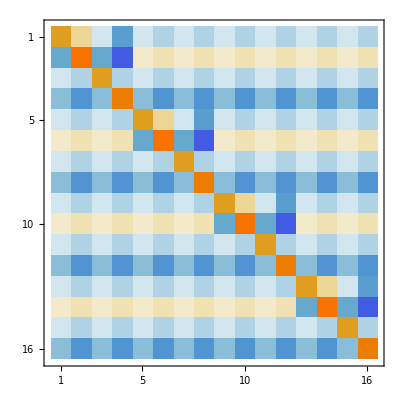
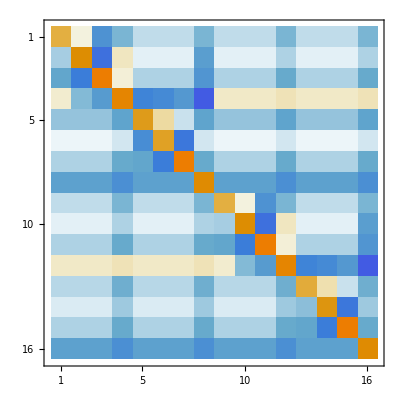
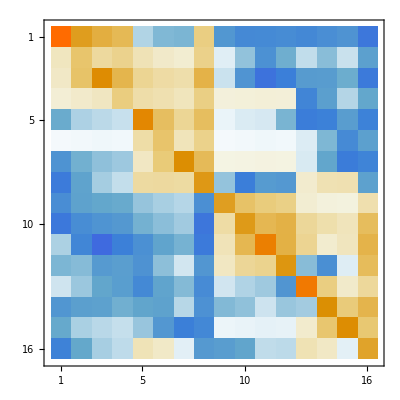
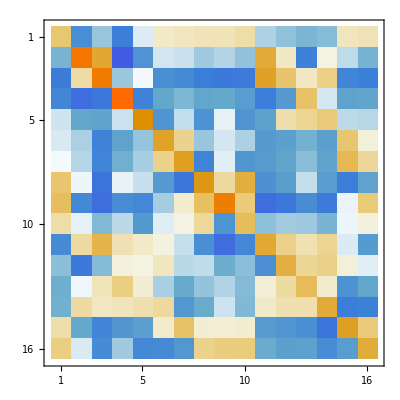
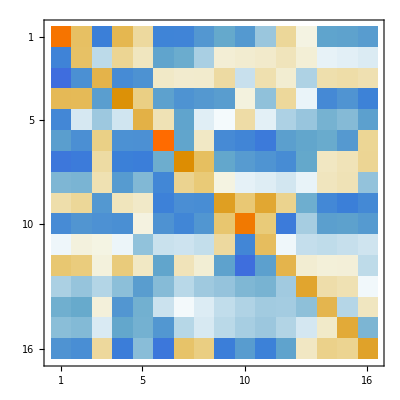
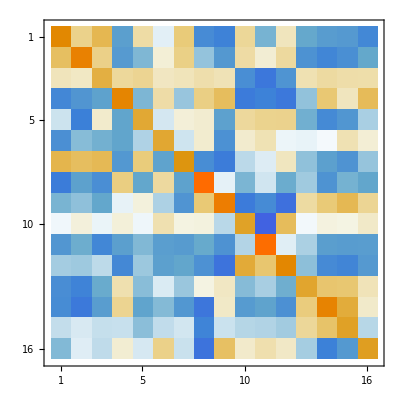
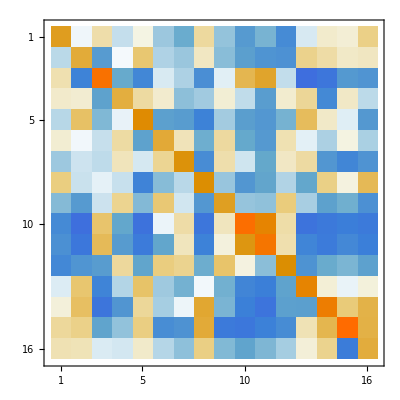
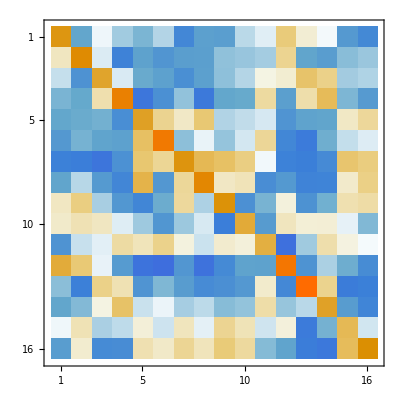
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#]&/@linearOperatorSeries
```

```mathematica
MatrixPlot[#]&/@laplacianSeries;
```